# Covariance

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: Small Dataset

```mathematica
dataSmall={{1,0},{3,2.5},{2,3},{0,2.5}};
```

```mathematica
μ=Mean[dataSmall]//N
```

{1.5,2.}

```mathematica
Covariance[dataSmall]//MatrixForm
```

(1.66667 | 0.5
0.5 | 1.83333)

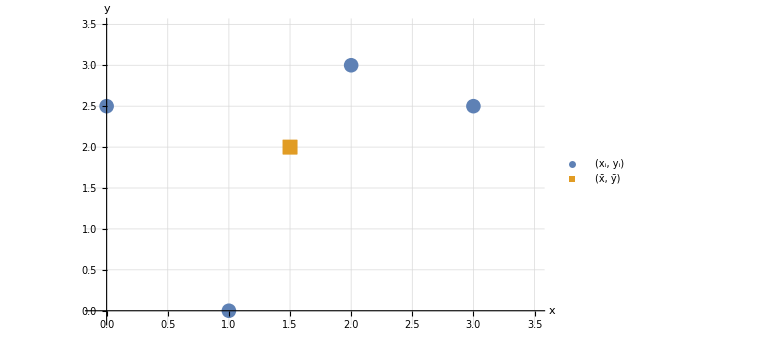

```mathematica
base=ListPlot[{dataSmall,{μ}},
PlotTheme->{"myTheme","ThickLines"},
GridLines->Automatic,
PlotRange->{{-0.1,3.51},{-0.1,3.5}},
AxesLabel->{it["x"],it["y"]},
PlotMarkers->{Automatic,15},
PlotLegends->{"(x_i, y_i)","(x̄, ȳ)"}
]
```

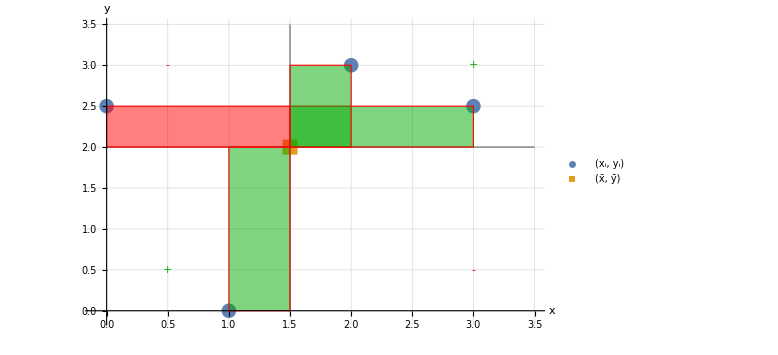

```mathematica
Show[
base,

Graphics[{
Gray,
Line[{{μ[[1]],0},{μ[[1]],3.5}}],
Line[{{0,μ[[2]]},{3.5,μ[[2]]}}],

Darker@Green,
FontSize->25,
Text["+",{3,3}],
Text["+",{0.5,0.5}],

Red,
Text["-",{3,0.5}],
Text["-",{0.5,3}],

EdgeForm[Thin],
Opacity[0.5],
Darker@Green,
Table[Rectangle[{Min[p[[1]],μ[[1]]],Min[p[[2]],μ[[2]]]},{Max[p[[1]],μ[[1]]],Max[p[[2]],μ[[2]]]}],{p,dataSmall[[{1,2,3}]]}],

Red,
Table[Rectangle[{Min[p[[1]],μ[[1]]],Min[p[[2]],μ[[2]]]},{Max[p[[1]],μ[[1]]],Max[p[[2]],μ[[2]]]}],{p,dataSmall[[{4}]]}]
}]
]
```

We can calculate the covariance by weighting the rectangles:

```mathematica
1/3(0.5*1+1.5*0.5+0.5*2-1.5*0.5)
```

0.5

## Part 2: Sign

The new datasets for the different signs may look like:

s_XY>0: positive line

s_XY=0: circle

s_XY<0: negative line

## Part 3: Large Dataset

```mathematica
SeedRandom[1337];
data=RandomVariate[MultinormalDistribution[{0,0},({{0.8, 0.5}, {0.5, 0.8}})],100];
data=(#1-Mean[data]&)/@data;
```

```mathematica
Covariance[data]//MatrixForm
```

(0.724658 | 0.37535
0.37535 | 0.71112)

```mathematica
dataPos=Cases[data,{x_,y_}/;x*y≥0];
dataNeg=Cases[data,{x_,y_}/;x*y<0];
```

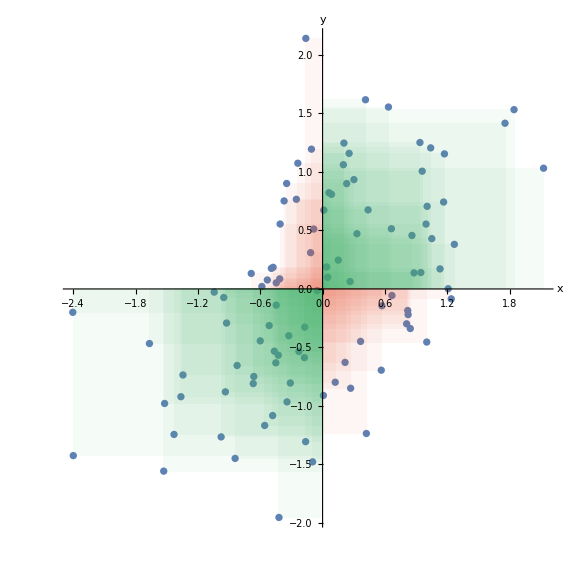

```mathematica
ListPlot[data,
PlotTheme->"myTheme",
AxesLabel->{"x","y"},
AspectRatio->1,
Epilog->{
{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],Opacity[0.05],(Rectangle[{0,0},#1]&)/@dataPos},
{RGBColor[0.915, 0.3325, 0.2125],Opacity[0.05],(Rectangle[{0,0},#1]&)/@dataNeg}
}
]
```

Increase: add a new point in the green area.

Increase even further: make sure that the new point is further away from the origin than the previous one.

The scaling of the features matters and if we change the units, the absolute value also changes (there is no normalization by the variances like for the correlation coefficient).